```mathematica
$MinPrecision=53;
```

### Defining The Domains

#### u Domain(s)

```mathematica
prec=64;
```

```mathematica
uOuterMin=1/10;
uOuterMax= 103/100;
uOuterDomains=3;
uOuterNodes=24;
uInnerNodes=12;
InterfaceNodes=Table[uOuterMin+i(uOuterMax-uOuterMin)/uOuterDomains,{i,0,uOuterDomains,1}];
```

```mathematica
InterfaceNodes//N
```

{0.1,0.41,0.72,1.03}

```mathematica
GetuDomain[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Flatten[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,2,uOutNodes}],{j,2,IntfaceNodes//Length}],1],prec];
Join[uInner,uOut]
]
```

```mathematica
uValues={{0.0,0.002025351319275129,0.00793732335844094,0.017256963302735746,0.02922924934990568,0.042884258086335746,0.05711574191366425,0.07077075065009432,0.08274303669726425,0.09206267664155907,0.09797464868072488,0.1},{0.09999999999999998,0.10144367836436871,0.10574782046109107,0.11283224826665475,0.12256499229529424,0.1347647499408149,0.1492042628011086,0.1656145500721956,0.1836899191516714,0.2030936601134971,0.22346431797684174,0.244422425928476,0.265577574071524,0.2865356820231582,0.30690633988650284,0.3263100808483286,0.3443854499278044,0.36079573719889135,0.37523525005918507,0.38743500770470574,0.3971677517333452,0.4042521795389089,0.40855632163563127,0.41000000000000003},{0.41,0.4114436783643687,0.41574782046109104,0.4228322482666548,0.4325649922952942,0.4447647499408149,0.4592042628011086,0.47561455007219555,0.4936899191516714,0.5130936601134971,0.5334643179768417,0.5544224259284759,0.5755775740715239,0.5965356820231582,0.6169063398865028,0.6363100808483285,0.6543854499278043,0.6707957371988913,0.685235250059185,0.6974350077047056,0.7071677517333451,0.7142521795389087,0.7185563216356312,0.72},{0.72,0.7214436783643687,0.7257478204610911,0.7328322482666547,0.7425649922952943,0.7547647499408149,0.7692042628011087,0.7856145500721956,0.8036899191516714,0.8230936601134972,0.8434643179768417,0.864422425928476,0.8855775740715239,0.9065356820231583,0.9269063398865028,0.9463100808483286,0.9643854499278044,0.9807957371988913,0.9952352500591851,1.0074350077047056,1.0171677517333453,1.0242521795389088,1.0285563216356313,1.03}};(*GetuDomain[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes]*);
```

```mathematica
uValues//Dimensions
```

{4}

#### x Domain

```mathematica
xMin=-750;
xMax=750;
xNodes=400;
Deltax=Abs[xMin-xMax]/xNodes;
xValues=Table[xMin+i Deltax,{i,0,xNodes-1}];
```

```mathematica
xValues
```

{-750,-2985/4,-1485/2,-2955/4,-735,-2925/4,-1455/2,-2895/4,-720,-2865/4,-1425/2,-2835/4,-705,-2805/4,-1395/2,-2775/4,-690,-2745/4,-1365/2,-2715/4,-675,-2685/4,-1335/2,-2655/4,-660,-2625/4,-1305/2,-2595/4,-645,-2565/4,-1275/2,-2535/4,-630,-2505/4,-1245/2,-2475/4,-615,-2445/4,-1215/2,-2415/4,-600,-2385/4,-1185/2,-2355/4,-585,-2325/4,-1155/2,-2295/4,-570,-2265/4,-1125/2,-2235/4,-555,-2205/4,-1095/2,-2175/4,-540,-2145/4,-1065/2,-2115/4,-525,-2085/4,-1035/2,-2055/4,-510,-2025/4,-1005/2,-1995/4,-495,-1965/4,-975/2,-1935/4,-480,-1905/4,-945/2,-1875/4,-465,-1845/4,-915/2,-1815/4,-450,-1785/4,-885/2,-1755/4,-435,-1725/4,-855/2,-1695/4,-420,-1665/4,-825/2,-1635/4,-405,-1605/4,-795/2,-1575/4,-390,-1545/4,-765/2,-1515/4,-375,-1485/4,-735/2,-1455/4,-360,-1425/4,-705/2,-1395/4,-345,-1365/4,-675/2,-1335/4,-330,-1305/4,-645/2,-1275/4,-315,-1245/4,-615/2,-1215/4,-300,-1185/4,-585/2,-1155/4,-285,-1125/4,-555/2,-1095/4,-270,-1065/4,-525/2,-1035/4,-255,-1005/4,-495/2,-975/4,-240,-945/4,-465/2,-915/4,-225,-885/4,-435/2,-855/4,-210,-825/4,-405/2,-795/4,-195,-765/4,-375/2,-735/4,-180,-705/4,-345/2,-675/4,-165,-645/4,-315/2,-615/4,-150,-585/4,-285/2,-555/4,-135,-525/4,-255/2,-495/4,-120,-465/4,-225/2,-435/4,-105,-405/4,-195/2,-375/4,-90,-345/4,-165/2,-315/4,-75,-285/4,-135/2,-255/4,-60,-225/4,-105/2,-195/4,-45,-165/4,-75/2,-135/4,-30,-105/4,-45/2,-75/4,-15,-45/4,-15/2,-15/4,0,15/4,15/2,45/4,15,75/4,45/2,105/4,30,135/4,75/2,165/4,45,195/4,105/2,225/4,60,255/4,135/2,285/4,75,315/4,165/2,345/4,90,375/4,195/2,405/4,105,435/4,225/2,465/4,120,495/4,255/2,525/4,135,555/4,285/2,585/4,150,615/4,315/2,645/4,165,675/4,345/2,705/4,180,735/4,375/2,765/4,195,795/4,405/2,825/4,210,855/4,435/2,885/4,225,915/4,465/2,945/4,240,975/4,495/2,1005/4,255,1035/4,525/2,1065/4,270,1095/4,555/2,1125/4,285,1155/4,585/2,1185/4,300,1215/4,615/2,1245/4,315,1275/4,645/2,1305/4,330,1335/4,675/2,1365/4,345,1395/4,705/2,1425/4,360,1455/4,735/2,1485/4,375,1515/4,765/2,1545/4,390,1575/4,795/2,1605/4,405,1635/4,825/2,1665/4,420,1695/4,855/2,1725/4,435,1755/4,885/2,1785/4,450,1815/4,915/2,1845/4,465,1875/4,945/2,1905/4,480,1935/4,975/2,1965/4,495,1995/4,1005/2,2025/4,510,2055/4,1035/2,2085/4,525,2115/4,1065/2,2145/4,540,2175/4,1095/2,2205/4,555,2235/4,1125/2,2265/4,570,2295/4,1155/2,2325/4,585,2355/4,1185/2,2385/4,600,2415/4,1215/2,2445/4,615,2475/4,1245/2,2505/4,630,2535/4,1275/2,2565/4,645,2595/4,1305/2,2625/4,660,2655/4,1335/2,2685/4,675,2715/4,1365/2,2745/4,690,2775/4,1395/2,2805/4,705,2835/4,1425/2,2865/4,720,2895/4,1455/2,2925/4,735,2955/4,1485/2,2985/4}

#### y Domain

```mathematica
yMin=-750;
yMax=750;
yNodes=400;
Deltay=Abs[yMin-yMax]/yNodes;
yValues=Table[yMin+i Deltay,{i,0,yNodes-1}];
```

```mathematica
yValues;
```

#### Grid

```mathematica
MyGrid=Table[{uValues[[i,u]],xValues[[x]],yValues[[y]]},{i,1,uValues//Length},{u,1,uValues[[i]]//Length},{x,1,xValues//Length},{y,1,yValues//Length}];
```

```mathematica
MyGrid//Dimensions
```

{4}

## Boosted Black Brain

## Inhomogeneous boosting

```mathematica
(*gdd=1/ρ^2 Table[ηdd[[u,v]]+,{u,1,4},{v,1,4}]*)
```

#### Random Factor

```mathematica
modesTot=2;
```

```mathematica
RandomCoefficients=Table[Random[],{i,1,modesTot}]
```

```mathematica
RandomCoefficients={0.1318694590540108,0.8790811465415185}
```

{0.131869,0.879081}

```mathematica
RandomDirections=Table[2{RandomReal[]-0.5,RandomReal[]-0.5},{i,1,modesTot}];
```

```mathematica
RandomOffsets=Table[Random[],{i,1,modesTot}]
```

```mathematica
RandomOffsets={0.3410781122223984,0.313461151042812}
```

{0.341078,0.313461}

```mathematica
ClearAll[RandomFactor]
```

```mathematica
RandomFactor[{x_,y_}]=Sum[RandomCoefficients[[i]] Cos[((i+1) 2 Pi (x(*{x,y}.RandomDirections[[i]]*))/(xMax-xMin)-(xMax-xMin)/(2 Pi (i+1)) (RandomOffsets[[i]]-0.5))] +Sin[((i+1) 2 Pi (y(*{x,y}.RandomDirections[[i]]*))/(xMax-xMin)-(xMax-xMin)/(2 Pi (i+1)) (RandomOffsets[[i]]-0.5))],{i,1,modesTot}];(*/;x<(xMax-xMin)/2&&y<(yMax-yMin)/2;
RandomFactor[{x_,y_}]=(Sum[RandomCoefficients[[i]] Cos[((i+2) 2 Pi ({x,y}.RandomDirections[[i]])/(xMax-xMin)-(xMax-xMin)/(2 Pi (i+1)) (RandomOffset-0.5))] ,{i,1,modesTot}])/;x>=(xMax-xMin)/2&&y<(yMax-yMin)/2;*)
```

```mathematica
NormFact=Max[Abs[(RandomFactor[{x,y}]//Minimize[#,{x,y}]&)[[1]]],(RandomFactor[{x,y}]//Maximize[#,{x,y}]&)[[1]]];
```

#### Boosting

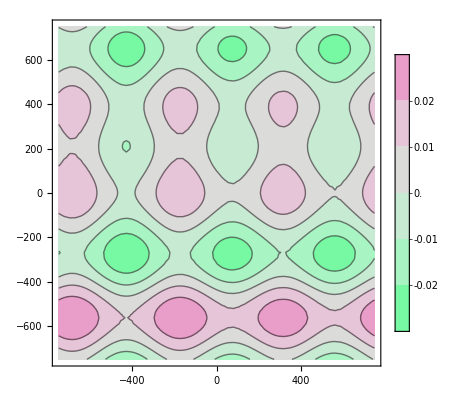

```mathematica
ContourPlot[1/100 RandomFactor[{x,y}],{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic,ColorFunction->"MintColors",MaxRecursion->3(*,PlotPoints->20*)]
```

```mathematica
ClearAll[u1d,u0d,u2d]
qx=(10Pi)/(xMax-xMin);
qy=Pi/(yMax-yMin);
(*u0d[x_,y_]=-2^(1/2);*)

u1d[x_,y_]:=(*0.1*)0.8Cos[qx y] +1/(30NormFact)RandomFactor[{x,y}];
u2d[x_,y_]:=0(*RandomFactor2[{x,y}]*);
b=1;
```

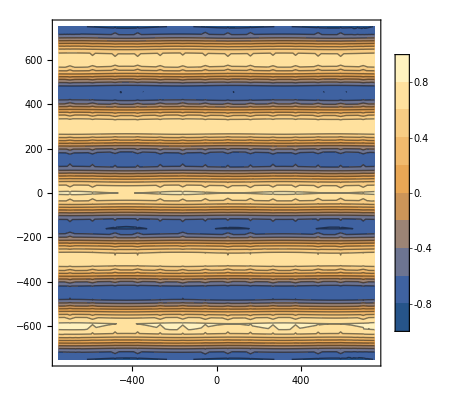

```mathematica
ContourPlot[u1d[x,y],{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic(*,ColorFunction->"TemperatureMap"*)(*,MaxRecursion->4*)(*,PlotPoints->20*)]
```

```mathematica
u0d[x_,y_]:=(*u2d[x,y]/.*)Solve[u1d[x,y]^2+u2d[x,y]^2-uu0d[x,y]^2==-1,uu0d[x,y]][[2,1,2]]
```

```mathematica
(*uofρ=NDSolve[{D[u[ρ],ρ]==(u[ρ]^2/ρ^2(1+(b ρ)^3(u1^2+u2^2))^(-1/2)),u[ϵ]==ϵ},u,{ρ,ϵ,1}][[1,1]];*)
```

```mathematica
(*ρofu=DSolve[{D[ρ[u,x,y],{u,1}]==(u^2/ρ[u,x,y]^2(1+(b ρ[u,x,y])^3(u1[x,y]^2+u2[x,y]^2))^(-1/2))^-1},ρ,{u,x,y}][[1,1]];*)
```

Here I compute r in function of rho. I set no boundary conditions for the ODE but I then impose the constant of integration to be zero

```mathematica
rofρ=DSolve[{D[r[ρ,x,y],{ρ}]==(-1/ρ^2(1+(b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2))(*,r[1]==1*)},r,{ρ,x,y}][[1,1]];
rofρ=r/.rofρ//N
```

Function[{ρ,x,y},1/ρ 1. Hypergeometric2F1[-0.333333,0.5,0.666667,-1. ρ^3 (0.8 Cos[0.020944 y]+0.0186604 (0.131869 Cos[18.9699+0.00837758 x]+0.879081 Cos[14.8443+0.0125664 x]+Sin[18.9699+0.00837758 y]+Sin[14.8443+0.0125664 y]))^2]+C[1][x,y]]

```mathematica
ContourPlot[rofρ[1,x,y]/.C[1][x,y]->0,{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic,ColorFunction->"TemperatureMap",MaxRecursion->5(*,PlotPoints->20*)]
```

-Graphics-

#### a3

Here I compute the initial data for a3. In the limit at infinity, ρ goes to zero, as u. Anyway, they don’t have the same asymptotic behaviour so we need to take the expansion of A, substitute u to its expression that depends on  ρ, and expand in terms of ρ around infinity (where ρ=0). In this way we have an expression of our variable in terms of ρ at infinity that has to match the expression for A in the Turbulence draft (Eq. 3.7).

```mathematica
AExp=1/u^2+u a3[t,u,x,y]+(2 ξ[t,x,y])/u+ξ[t,x,y]^2-2 Derivative[1,0,0][ξ][t,x,y];
```

```mathematica
AExpOfρ=AExp/.u->rofρ[ρ,x,y]^-1(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,1}]&;
```

```mathematica
(*AExpOfρ//Normal//Simplify*)
```

```mathematica
AToMatch=ρ^-2(1-(b ρ)^3(1+u1d[x,y]^2+u2d[x,y]^2))//Simplify
```

1/ρ^2-ρ (1+(0.8 Cos[(π y)/150]+0.0186604 (0.131869 Cos[18.9699+0.00837758 x]+0.879081 Cos[14.8443+0.0125664 x]+Sin[18.9699+0.00837758 y]+Sin[14.8443+0.0125664 y]))^2)

```mathematica
(*AExpOfρ//Normal//Simplify*)
```

Let' s look for ξ

```mathematica
c1Rule=Solve[Coefficient[AExpOfρ,1/ρ]==Coefficient[AToMatch,1/ρ],  C[1][x,y]]//Flatten
```

{C[1][x,y]→-1. ξ[t,x,y]}

Does this work with order term (it has to be checked for every configuration)???

```mathematica
(*SeriesCoefficient[AExpOfρ,{ρ,0,0}]/.c1Rule*)
```

xi can’t depend on t

```mathematica
Coefficient[AToMatch,ρ]
```

-1-(0.8 Cos[(π y)/150]+0.0186604 (0.131869 Cos[18.9699+0.00837758 x]+0.879081 Cos[14.8443+0.0125664 x]+Sin[18.9699+0.00837758 y]+Sin[14.8443+0.0125664 y]))^2

```mathematica
Coefficient[AExpOfρ,ρ]
```

1. a3[t,0,x,y]+0.5 (0.8 Cos[0.020944 y]+0.0186604 (0.131869 Cos[18.9699+0.00837758 x]+0.879081 Cos[14.8443+0.0125664 x]+Sin[18.9699+0.00837758 y]+Sin[14.8443+0.0125664 y]))^2

I compare the same order coefficient of ρ

```mathematica
a3Rule =Solve[Coefficient[AToMatch,ρ]==Coefficient[AExpOfρ,ρ],a3[t,0,x,y]][[1]]
```

{a3[t,0,x,y]→-1. (1.+1.5 (0.8 Cos[0.020944 y]+0.0186604 (0.131869 Cos[18.9699+0.00837758 x]+0.879081 Cos[14.8443+0.0125664 x]+Sin[18.9699+0.00837758 y]+Sin[14.8443+0.0125664 y]))^2)}

From Chasler paper a3 should be

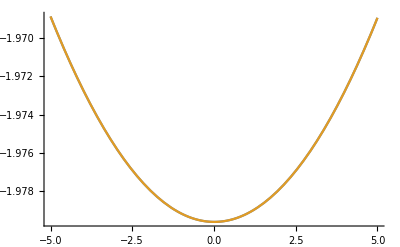

```mathematica
Plot[{-1/2(-1+3 u0d[0.59,y]^2)//Simplify,a3[t,0,x,y]/.a3Rule/.x->0.59},{y,-5,5}]
```

Export a3 Initial data

```mathematica
a3Data=Table[(a3[t,0,x,y]/.a3Rule/.x->xValues[[i]]/.y->yValues[[j]])(*(1+(RandomReal[]-0.5)/100)*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
ListContourPlot[a3Data,PlotLegends->Automatic]
```

-Graphics-

```mathematica
a3AttributesAndData={"a3"->a3Data};
```

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5",a3AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5

```mathematica
Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5","Data"]//Keys
```

{/a3}

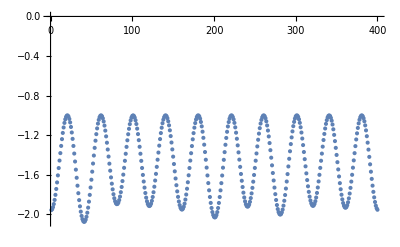

```mathematica
ListPlot[Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5","Data"][[1,1]]]
```

#### f1

Same procedure as above but for F1.

```mathematica
FExp=u f1[t,z,y]+Derivative[0,1,0][ξ][t,x,y];
```

```mathematica
FExpOfρ=FExp/.u->rofρ[ρ,x,y]^-1(*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,4}]&;
```

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

Chasler paper

```mathematica
FToMatch=-(b ρ(*ofu[{0,x,y}]*))^3/(ρ(*ofu[{0,x,y}]*))^2 u0d[x,y] u1d[x,y];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
-(b ρ(*ofu[{0,x,y}]*))^3/(ρ(*ofu[{0,x,y}]*))^2 u0d[x,y] u1d[x,y]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-1.41085×10^-25 ρ √(5.02385×10^49+3.04204×10^44 Cos[18.9699+0.00837758 x]^2+4.05583×10^45 Cos[18.9699+0.00837758 x] Cos[14.8443+0.0125664 x]+1.35187×10^46 Cos[14.8443+0.0125664 x]^2+1.97798×10^47 Cos[18.9699+0.00837758 x] Cos[0.020944 y]+1.31858×10^48 Cos[14.8443+0.0125664 x] Cos[0.020944 y]+3.21527×10^49 Cos[0.020944 y]^2+4.61372×10^45 Cos[18.9699+0.00837758 x] Sin[18.9699+0.00837758 y]+3.07564×10^46 Cos[14.8443+0.0125664 x] Sin[18.9699+0.00837758 y]+1.49995×10^48 Cos[0.020944 y] Sin[18.9699+0.00837758 y]+1.74935×10^46 Sin[18.9699+0.00837758 y]^2+4.61372×10^45 Cos[18.9699+0.00837758 x] Sin[14.8443+0.0125664 y]+3.07564×10^46 Cos[14.8443+0.0125664 x] Sin[14.8443+0.0125664 y]+1.49995×10^48 Cos[0.020944 y] Sin[14.8443+0.0125664 y]+3.4987×10^46 Sin[18.9699+0.00837758 y] Sin[14.8443+0.0125664 y]+1.74935×10^46 Sin[14.8443+0.0125664 y]^2) (0.8 Cos[(π y)/150]+0.0186604 (0.131869 Cos[18.9699+(π x)/375]+0.879081 Cos[14.8443+(π x)/250]+Sin[18.9699+(π y)/375]+Sin[14.8443+(π y)/250]))

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
fxRule=Solve[Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ],f1[t,z,y]]//Simplify
```

{{f1[t,z,y]→(-3.47173×10^-28 Cos[18.9699+0.00837758 x]-2.31436×10^-27 Cos[14.8443+0.0125664 x]-1.12868×10^-25 Cos[0.020944 y]-2.6327×10^-27 Sin[18.9699+0.00837758 y]-2.6327×10^-27 Sin[14.8443+0.0125664 y]) √(5.02385×10^49+3.04204×10^44 Cos[18.9699+0.00837758 x]^2+1.35187×10^46 Cos[14.8443+0.0125664 x]^2+3.21527×10^49 Cos[0.020944 y]^2+1.49995×10^48 Cos[0.020944 y] Sin[18.9699+0.00837758 y]+1.74935×10^46 Sin[18.9699+0.00837758 y]^2+1.49995×10^48 Cos[0.020944 y] Sin[14.8443+0.0125664 y]+3.4987×10^46 Sin[18.9699+0.00837758 y] Sin[14.8443+0.0125664 y]+1.74935×10^46 Sin[14.8443+0.0125664 y]^2+Cos[18.9699+0.00837758 x] (4.05583×10^45 Cos[14.8443+0.0125664 x]+1.97798×10^47 Cos[0.020944 y]+4.61372×10^45 Sin[18.9699+0.00837758 y]+4.61372×10^45 Sin[14.8443+0.0125664 y])+Cos[14.8443+0.0125664 x] (1.31858×10^48 Cos[0.020944 y]+3.07564×10^46 Sin[18.9699+0.00837758 y]+3.07564×10^46 Sin[14.8443+0.0125664 y]))}}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

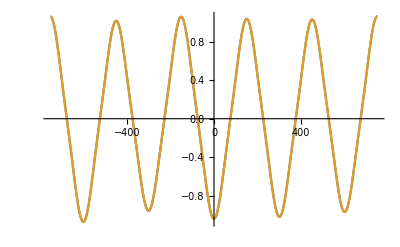

```mathematica
Plot[{-u0d[1.48,y] u1d[1.48,y],fxRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

```mathematica
DSolve[SeriesCoefficient[FToMatch,{ρ,0,0}]==SeriesCoefficient[FExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,y]]}

ξ can’t depend on x!

Export fx initial data

```mathematica
fxData=Table[((f1[t,z,y]/.fxRule[[1]])/.x->xValues[[i]]/.y->yValues[[j]])(*(1+(RandomReal[]-0.5)/100)*),{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
(*fxRule*)
```

```mathematica
fxData//Dimensions
```

{400,400}

```mathematica
ListPlot3D[fxData]
```

-Graphics3D-

```mathematica
fxAttributesAndData={"fx"->fxData};
```

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5",fxAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5

#### f2

Same procedure as above but for F1.

```mathematica
F2Exp=u f2[t,z,y]+Derivative[0,0,1][ξ][t,x,y];
```

```mathematica
F2ExpOfρ=F2Exp/.u->rofρ[ρ,x,y]^-1(*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,4}]&;
```

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
(*Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]*)
```

Chasler paper

```mathematica
F2ToMatch=-(b ρ(*ofu[{0,x,y}]*))^3/(ρ(*ofu[{0,x,y}]*))^2 u0d[x,y] u2d[x,y];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ]*)
```

```mathematica
fyRule=Solve[Coefficient[F2ToMatch,ρ]==Coefficient[F2ExpOfρ,ρ],f2[t,z,y]]//Simplify
```

{{f2[t,z,y]→0.}}

From Chasler paper this should be.

```mathematica
(*-u0d[x,y] u1d[x,y]*)
```

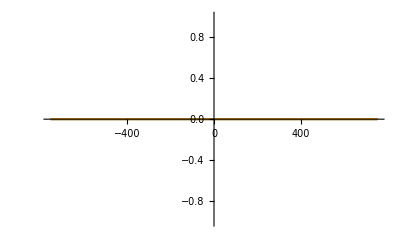

```mathematica
Plot[{-u0d[1.48,y] u2d[1.48,y],fyRule[[1,1,2]]/.x->1.48},{y,yMin,yMax}]
```

```mathematica
DSolve[SeriesCoefficient[F2ToMatch,{ρ,0,0}]==SeriesCoefficient[F2ExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,x]]}

ξ can’t depend on x!

Export fx initial data

```mathematica
fyData=Table[(f2[t,z,y]/.fyRule[[1]])/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
(*fxRule*)
```

```mathematica
fyData//Dimensions
```

{400,400}

```mathematica
ListPlot3D[fyData]
```

-Graphics3D-

```mathematica
fyAttributesAndData={"fy"->fyData};
```

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfy_BBB.h5",fyAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfy_BBB.h5

```mathematica
(*Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5","Data"]*)
```

### B Function

#### Grid For ρ

The initial data for B is different, since B is defined through the entire domain. We need to invert the function r(ρ). This is a problem, since that is not invertible analytically.

```mathematica
ClearAll[uofρ]
```

```mathematica
(*uofρ[ρs_,xs_,ys_]:=rofρ[[2]]^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys*)
```

```mathematica
uofρ=Function[{ρs,xs,ys},rofρ[[2]]^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys]
```

Function[{ρs,xs,ys},1/rofρ⟦2⟧/.c1Rule⟦1⟧/.ξ→Function[{t,x,y},0]/.ρ→ρs/.x→xs/.y→ys]

Horizon location

```mathematica
Minimize[uofρ[1,x,y],{x,y(*,xMin,xMax*)}][[1]]//FullForm
Maximize[uofρ[1,x,y],{x,y(*,xMin,xMax*)}][[1]]//Print
```

0.872132

1.

```mathematica
Plot3D[uofρ[1,x,y],{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic,
(*PlotRange->All,*)(*MaxRecursion->4,*)ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
(*uofρToInt=ParallelTable[{MyGrid[[i,j,k]],uofρ[MyGrid[[i,j,k]][[1]],MyGrid[[i,j,k]][[2]],MyGrid[[i,j,k]][[3]]]},{i,1,MyGrid//Length},{j,1,MyGrid[[1]]//Length},{k,1,MyGrid[[1,1]]//Length}];//AbsoluteTiming*)
```

```mathematica
(*ρofuOld2=InverseFunction[Function[{ρ,x,y},Intuofρ[ρ,x,y]],1,3];*)
```

```mathematica
ρofuOld=InverseFunction[Function[{ρ,x,y},uofρ[ρ,x,y]],1,3];
```

```mathematica
ClearAll[ρofu,ρofu2]
```

```mathematica
ρofu=Function[C,ρofuOld[C[[1]],C[[2]],C[[3]]]]
```

Function[C,ρofuOld[C⟦1⟧,C⟦2⟧,C⟦3⟧]]

```mathematica
(*ρofu2=Function[C,ρofuOld2[C[[1]],C[[2]],C[[3]]]]*)
```

```mathematica
(*ListPlot[{uValues[[uInnerNodes;;]],Table[ρofu[{uValues[[i]]//N,xMin,yMin}],{i,uInnerNodes,uValues//Length}]}//Transpose(*,{x,-5,5}*),PlotRange->All]*)
```

```mathematica
(*ListPlot[{uValues[[uInnerNodes;;]],Table[ρofu2[{uValues[[i]],xMin,yMin}],{i,uInnerNodes,uValues//Length}]}//Transpose(*,{x,-5,5}*),PlotRange->All]*)
```

```mathematica
(*ParallelTable[ρofu2[MyGrid[[1,j,k]]](*,{i,1,uValues//Length}*),{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming*)
```

```mathematica
MyGrid//Dimensions
```

{4}

```mathematica
ρofuValues=ParallelTable[ρofu[MyGrid[[n,i,j,k]]],{n,1,uValues//Length},{i,1,uValues[[n]]//Length},{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming
```

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/13.2/Executables/wolfram -noinit -subkernel -wstp,1638,44].

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/13.2/Executables/wolfram -noinit -subkernel -wstp,1639,45].

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/13.2/Executables/wolfram -noinit -subkernel -wstp,1640,46].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Parallel`Developer`ConnectKernel::failinit: 4 of 10 kernels failed to initialize.

```mathematica
ρofuValues//Dimensions
```

{4}

```mathematica
u1Values=Table[u1d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.040168,Null}

```mathematica
u2Values=Table[u2d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.002049,Null}

```mathematica
u0Values=Table[u0d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{1.55817,Null}

#### B Function

```mathematica
ClearAll[InitialBAnalytic]
```

```mathematica
InitialBAnalytic[u_,x_,y_]:=-1/2 Log[(1+(b ρofu[{u,x,y}])^3 u1d[x,y]^2)/(1+(b ρofu[{u,x,y}])^3 u2d[x,y]^2)] u^-3;
```

```mathematica
InitialB1=ParallelTable[N[SeriesCoefficient[InitialBAnalytic[u,xValues[[i]],yValues[[j]]],{u,uValues[[1,1]],0}]//Normal](*(1+ (RandomReal[]-0.5)/200)*),{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{133.452,Null}

```mathematica
InitialB=ParallelTable[N[-1/2 Log[(1+(b ρofuValues[[n,ui,xi,yi]])^3 u1Values[[xi,yi]]^2)/(1+(b ρofuValues[[n,ui,xi,yi]])^3 u2Values[[xi,yi]]^2)] uValues[[n,ui]]^-3,$MinPrecision](*(1+(RandomReal[]-0.5)/200)*),{n,1,uValues//Length},{ui,1,uValues[[n]]//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
InitialB[[1,1]]=InitialB1(*Table[-0.5,{i,1,25},{j,1,25}]*);
(*InitialB[[1]]=InitialB[[2]];*)
```

Power::infy: Infinite expression 1/0.^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{0.721265,Null}

```mathematica
(*Table[InitialB[[1,i,j]]=-u1d[xValues[[i]],yValues[[j]]]^2/2,{i,1,xValues//Length},{j,1,yValues//Length}];*)
```

```mathematica
(*ListContourPlot[InitialB[[1]],PlotLegends->Automatic]*)
```

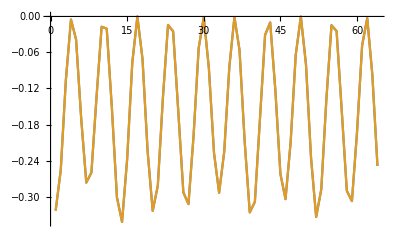

```mathematica
ListPlot[{InitialB[[1,1,1,;;]],Table[-u1d[xValues[[1]],yValues[[i]]]^2/2(*-InitialB[[1,1,i]]*),{i,1,yValues//Length}]},Joined->True(*,PlotStyle->{Dashed,Dotted}*)]
```

```mathematica
(*phiFunc=InterpolatingFunction[…]*)
```

```mathematica
(*phi=Table[phiFunc[uValues[[i]]],{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];*)
```

```mathematica
(*ExportData=Join[{InitialB(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialB(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming*)
```

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
(*AttributesAndData=Table[ExportAttributes[[i]]->ExportData[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming*)
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->InitialB[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.003539,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5

```mathematica
Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5","Data"][[1]]//Dimensions
```

{24,64,64}

#### B2 Function

```mathematica
Maxg=FindMaxValue[{Abs[InterpolatingFunction[…][z]//Re],0<=z<=1},z];
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

InterpolatingFunction::dmval: Input value {-0.0000320803} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0000260249} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.000113482} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
ExpOfHxy[tt_,u_]:=E^(-ⅈ ω (tt-ArcTan[u]/2+1/4 Log[1-u]-1/4 Log[1+u]))/.ω->4.763570116920460863I
```

```mathematica
Parametricgxy[u_]:=1/20 ExpOfHxy[0,u]InterpolatingFunction[…][u]/Maxg//Re;
```

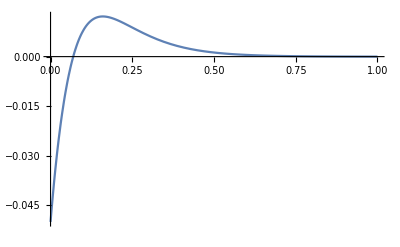

```mathematica
Plot[Parametricgxy[u],{u,0,1},PlotRange->All]
```

```mathematica
Series[-Log[(1-4 a^2 u^8)^(1/6)]/u^4,{u,0,4}]
```

(2 a^2 u^4)/3+O[u]^5

```mathematica
Solve[{S^2 E^(-u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(-u^4 B2in)Sinh[u^4 Gin]==2 u^2 a,S^2 E^(2 u^4 B2in)==u^-2},{S,Gin,B1in,B2in}]/. C[1]->0/. C[2]->0/.C[3]->0
```

{{S→-((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(1-4 a^2 u^8)^(1/6)]/u^4},{S→-((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(1-4 a^2 u^8)^(1/6)]/u^4},{S→-((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(1-4 a^2 u^8)^(1/6)]/u^4},{S→-((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(1-4 a^2 u^8)^(1/6)]/u^4},{S→((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(1-4 a^2 u^8)^(1/6)]/u^4},{S→((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(1-4 a^2 u^8)^(1/6)]/u^4},{S→((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(1-4 a^2 u^8)^(1/6)]/u^4},{S→((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(1/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(-1)^(1/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→-((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→-(ⅈ π)/u^4,B2in→-Log[-(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4},{S→((-1)^(2/3) (1-4 a^2 u^8)^(1/6))/u,Gin→Log[(√(1-4 a^2 u^8)+2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[-(-1)^(2/3) (1-4 a^2 u^8)^(1/6)]/u^4}}

```mathematica
InitialB2=ParallelTable[N[-Log[(1-4 a^2 u^8)^(1/6)]/u^4/.a->Parametricgxy[uValues[[ui]]]/.u->uValues[[ui]],$MinPrecision],{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {1.024491681045681953601531004276832149691709130880192856967105393} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.052920196832761605015795291404792005793337833604905915370574892} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.024491681045681953601531004276832149691709130880192856967105393} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.052920196832761605015795291404792005793337833604905915370574892} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.024491681045681953601531004276832149691709130880192856967105393} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.052920196832761605015795291404792005793337833604905915370574892} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.07491006586389132885131328238047473284403663414797247068004738} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.090148683402318070379897764154224147285293185095574613420011428} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.098419419507347924414986400827153106268867738622415312382752078} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.002158282635382400086941442423348516223148347131070448252196111} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{186.73,Null}

```mathematica
InitialB2uzero=ParallelTable[0,{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{0.012855,Null}

{0.018013,Null}

```mathematica
InitialB2[[1]]=InitialB2uzero;
```

```mathematica
ExportDataB2=Join[{InitialB2(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialB2(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

{0.000253,Null}

```mathematica
ExportAttributesB2=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndDataB2=Table[ExportAttributesB2[[i]]->ExportDataB2[[i]],{i,1,ExportAttributesB2//Length}];//AbsoluteTiming
```

{0.003247,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB2_BBB.h5",AttributesAndDataG,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB2_BBB.h5

#### G Function

```mathematica
Maxg=FindMaxValue[{Abs[InterpolatingFunction[…][z]//Re],0<=z<=1},z];
```

$MinPrecision::preccon: Cannot set $MinPrecision such that $MaxPrecision < $MinPrecision.

InterpolatingFunction::dmval: Input value {-0.0000320803} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0000260249} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.000113482} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
ExpOfHxy[tt_,u_]:=E^(-ⅈ ω (tt-ArcTan[u]/2+1/4 Log[1-u]-1/4 Log[1+u]))/.ω->4.763570116920460863I
```

```mathematica
Parametricgxy[u_]:=1/20 ExpOfHxy[0,u]InterpolatingFunction[…][u]/Maxg//Re;
```

```mathematica
Plot[Parametricgxy[u],{u,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Series[Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,{u,0,4}]
```

2 a+O[u]^5

```mathematica
Solve[{S^2 E^(-u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(u^4 B1in-u^4 B2in)Cosh[u^4 Gin]==u^-2,S^2 E^(-u^4 B2in)Sinh[u^4 Gin]==2 u^2 a,S^2 E^(2 u^4 B2in)==u^-2},{S,Gin,B1in,B2in}][[1]]/. C[1]->0/. C[2]->0/.C[3]->0
```

{S→-((1-4 a^2 u^8)^(1/6))/u,Gin→Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4,B1in→0,B2in→-Log[(1-4 a^2 u^8)^(1/6)]/u^4}

```mathematica
InitialG=ParallelTable[N[Log[(-√(1-4 a^2 u^8)-2 a u^4 √(1-4 a^2 u^8))/(-1+4 a^2 u^8)]/u^4/.a->Parametricgxy[uValues[[ui]]]/.u->uValues[[ui]],$MinPrecision],{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];//AbsoluteTiming
```

Power::infy: Infinite expression 1/0^4 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^4 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^4 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.024491681045681953601531004276832149691709130880192856967105393} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.052920196832761605015795291404792005793337833604905915370574892} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.07491006586389132885131328238047473284403663414797247068004738} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.090148683402318070379897764154224147285293185095574613420011428} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.098419419507347924414986400827153106268867738622415312382752078} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.002158282635382400086941442423348516223148347131070448252196111} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{200.882,Null}

```mathematica
InitialG1=ParallelTable[2a/.a->Parametricgxy[uValues[[1]]],{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{2.61441,Null}

```mathematica
InitialG[[1]]=InitialG1;
```

```mathematica
ExportDataG=Join[{InitialG(*phi*)[[;;uInnerNodes,;;,;;]]},Table[InitialG(*phi*)[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

{0.000213,Null}

```mathematica
ExportAttributesG=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndDataG=Table[ExportAttributesG[[i]]->ExportDataG[[i]],{i,1,ExportAttributesG//Length}];//AbsoluteTiming
```

{0.000027,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialG_BBB.h5",AttributesAndDataG,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialG_BBB.h5

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialG_BBB.h5

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialG_BBB.h5

#### ϕ Function

```mathematica
(*Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialphi_BB.h5",AttributesAndData,"Datasets"]*)
```

```mathematica
testImport=Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5","Data"]
```